LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

开始扫描两体纠缠态参数...

扫描完成，总耗时：46 秒

扫描结果（α 与最大 L）：

α | Max L
0 | 1.
π/60 | 1.00545
π/30 | 1.02138
π/20 | 1.04666
π/15 | 1.07955
π/12 | 1.11803
π/10 | 1.15995
(7 π)/60 | 1.20322
(2 π)/15 | 1.2459
(3 π)/20 | 1.28628
π/6 | 1.32288
(11 π)/60 | 1.35446
π/5 | 1.38004
(13 π)/60 | 1.39885
(7 π)/30 | 1.41035
π/4 | 1.41421
(4 π)/15 | 1.41035
(17 π)/60 | 1.39885
(3 π)/10 | 1.38004
(19 π)/60 | 1.35446
π/3 | 1.32288
(7 π)/20 | 1.28628
(11 π)/30 | 1.2459
(23 π)/60 | 1.20322
(2 π)/5 | 1.15995
(5 π)/12 | 1.11803
(13 π)/30 | 1.07955
(9 π)/20 | 1.04666
(7 π)/15 | 1.02138
(29 π)/60 | 1.00545
π/2 | 1.

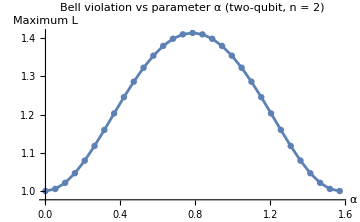

```mathematica
(* ==========1. 基本定义==========*)ClearAll["Global`*"];
LaunchKernels[];

(*Pauli 矩阵*)
sigma[1]=PauliMatrix[1];
sigma[2]=PauliMatrix[2];
sigma[3]=PauliMatrix[3];

(*单量子比特测量算符 n·σ*)
measurement[θ_,ϕ_]:=Module[{n={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}},n.{sigma[1],sigma[2],sigma[3]}];

(*两体关联函数，显式传入态向量*)
correlation[psi_][A_,B_]:=Conjugate[psi].(KroneckerProduct[A,B].psi);

(* ==========2. Bell 表达式与优化辅助==========*)
(*用户可自行修改 n 和系数矩阵 coeff*)
n=2;  (*每人的测量数量*)

(*系数矩阵 coeff，规模 n×n，定义 Bell 表达式：S=Sum_{i,j} coeff[[i,j]]* <A_i B_j>经典界限 classicalBound 需根据选用的不等式手动设定*)
coeff={{1,-1},{1,1}};
classicalBound=2;                 (* 经典界限*)

(*计算 Bell 表达式 S*)
bellExpression[opsA_,opsB_,psi_]:=Sum[coeff[[i,j]]*correlation[psi][opsA[[i]],opsB[[j]]],{i,n},{j,n}];

(*将角度二维数组转为测量算符列表*)
makeMeasurements[angles_]:=Map[measurement@@#&,angles,{1}];

(*从 4 n 个优化变量还原两人的角度组（每人 n 种测量×2 个角度）*)
anglesFromVars[varList_List]:=Module[{a,b},a=Partition[varList[[1;;2 n]],2];(*A1..An*)b=Partition[varList[[2 n+1;;4 n]],2];(*B1..Bn*){a,b}];

(*从变量生成两组测量算符*)
opsFromVars[varList_List]:=Module[{anglesA,anglesB},{anglesA,anglesB}=anglesFromVars[varList];
{makeMeasurements[anglesA],makeMeasurements[anglesB]}];

(*目标函数 L= |S| /classicalBound，经典最大值≤1*)
target[varList_List,psi_]:=Module[{opsA,opsB},{opsA,opsB}=opsFromVars[varList];
Abs[bellExpression[opsA,opsB,psi]]/classicalBound];

(* ==========3. 对固定态求最大违反值的函数==========*)
maxLForState[psi_]:=Module[{vars,cons,maxVal,optVars},(*4 n 个角度变量：每人 n 种测量，每种测量 θ,ϕ*)vars=Flatten[Table[{θA[i],ϕA[i],θB[i],ϕB[i]},{i,n}]];
(*角度范围约束*)cons=Flatten[Table[{0<=θA[i]<=Pi,0<=ϕA[i]<=2 Pi,0<=θB[i]<=Pi,0<=ϕB[i]<=2 Pi},{i,n}]];
(*全局优化*){maxVal,optVars}=NMaximize[{target[vars,psi],cons},vars,Method->"DifferentialEvolution",MaxIterations->1000,AccuracyGoal->5,PrecisionGoal->5];
maxVal   (*返回最大 L*)]

(* ==========4. 参数化两体纠缠态并循环扫描==========*)
(* |ψ(α)> =cosα|00>+sinα|11>，α∈[0,π/2]*)
twoQubitState[α_]:=Normalize[{Cos[α],0,0,Sin[α]}];

(*扫描范围*)
αRange=Subdivide[0,Pi/2,30];   (*0 到 π/2 等分 30 份，共 31 个点*)

(*扫描部分，带进度条和计时*)
Print["开始扫描两体纠缠态参数..."];
totalSteps=Length[αRange];
step=0;
startTime=AbsoluteTime[];

results=Monitor[ParallelTable[currentPsi=twoQubitState[α];
maxL=maxLForState[currentPsi];
step++;
{α,maxL},{α,αRange}],Grid[{{"进度：" ProgressIndicator[step/totalSteps]},{Row[{step,"/",totalSteps}]},{Row[{"已用时：",Round[AbsoluteTime[]-startTime]," 秒"}]}},Alignment->Left]];

endTime=AbsoluteTime[];
Print["扫描完成，总耗时：",Round[endTime-startTime]," 秒"];

(*结果展示*)
Print["扫描结果（α 与最大 L）："];
Print[TableForm[results,TableHeadings->{None,{"α","Max L"}}]];

(*绘制曲线*)
ListPlot[results,Joined->True,Mesh->All,AxesLabel->{"α","Maximum L"},PlotLabel->"Bell violation vs parameter α (two-qubit, n = "<>ToString[n]<>")",ImageSize->Medium]
```